```mathematica
Clear["`*"]
```

```mathematica
<<PlotLegends`
```

# Spencer Lyon

## Physics 330

Lab 1

## P1.2

```mathematica
test = {L ->  0.001,  R -> 100, emf -> 6};
eqn = L * D[i[t],t] + R * i[t] == emf;
ans = DSolve[{eqn,i[0]==0},i[t],t];
curr = i[t]/.ans[[1]];
Manipulate[Plot[curr/.test, {t, -high/100,high}, PlotRange->{-0.02,.06}],{{high , 0.000116}, 0.000001,.001, (.001/100/2)}]
```

ReplaceAll::reps: TraditionalForm`{test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

## P1.3

### a.) Solving Bessel’s Equation

```mathematica
besselsEquation = x^2 * D[f[x], {x,2}] + x * D[f[x], {x,1}] + (x^2 - n^2) * f[x]==0;
DSolve[besselsEquation, f[x],x]
```

{{f(x)→c_1 nx+c_2 nx}}

### b.) Solving Legendre’s Equation

```mathematica
legendresEquation = ((1 - x^2) * D[f[x], {x, 2}] - 2 * x * D[f[x], {x,1}] + n * (n + 1)* f[x] == 0);
DSolve[legendresEquation, f[x],x]
```

{{f(x)→c_1 nx+c_2 nx}}

{{f(x)→c_1 nx+c_2 nx}}

## P1.4

### a.) Initial Velocity needed to go to the moon.

11088.6

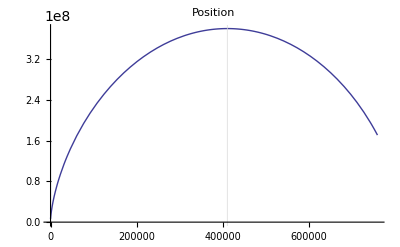

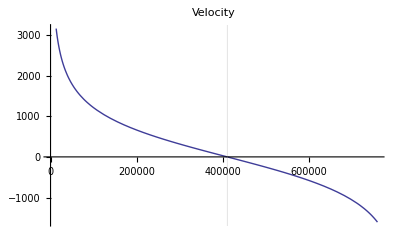

The max height is 3.8×10^8 and it took 410900. seconds to get there

The initial velocity that was needed to do this was 11088.6 m/s

```mathematica
initialV = 11.088561 10^3
eqnsMoon={z'[t]==v[t],v'[t]==-G*M/z[t]^2,v[0]==v0,z[0]==z0};
testMoon={M->6 10^24 ,G->6.67×10^-11, v0->initialV,z0->6.4 10^6};
tmin = 0 ;tmax =800000;
nsols = NDSolve[eqnsMoon/.testMoon, {z[t], v[t]}, {t, tmin, tmax}];
position = z[t]/.nsols[[1]];
velocity = v[t]/. nsols[[1]];
sol= Quiet[FindRoot[velocity, {t,290000}]];
ht = t/. sol;
height = position /. sol;
Plot[{position},{t,0, tmax - tmax*.05}, PlotLabel->"Position", GridLines->{{ht},{}}]
Plot[velocity, {t, 0, tmax - tmax*.05}, PlotLabel->"Velocity", GridLines->{{ht},{}}]
Print["The max height is ", height, " and it took ", ht, " seconds to get there"]
Print["The initial velocity that was needed to do this was ", initialV, " m/s"]
```

### b.) Symbolic try then success numerically

```mathematica
hardEqn = D[y[x], {x,2}] == Sin[ π * y[x]/x];
```

```mathematica
DSolve[hardEqn, y[x],x]
```

DSolve[y''(x)==sin((π y(x))/x),y(x),x]

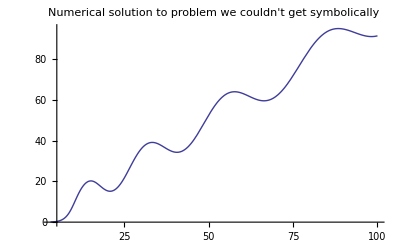

```mathematica
hardSystem = {D[y[x],x] == z[x], D[z[x],x] == Sin[π * y[x]/x], y[1]==y1, z[1]==z1};
testCase = {z1->0.01, y1->0};
xmin = π -  1;xmax = 105;
nsol = NDSolve[hardSystem/.testCase,{z[x],y[x]},{x,xmin,xmax}];
yPosition = y[x]/.nsol;
Plot[yPosition, {x, π, 100}, PlotLabel->"Numerical solution to problem we couldn't get symbolically"]
```

## P1.5

### a.) Solving the baseball system

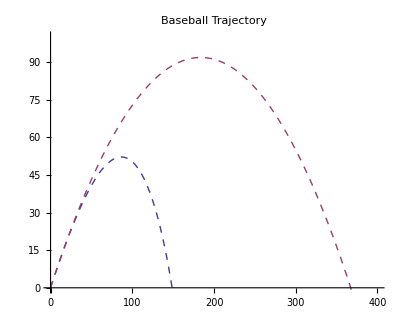

The ball travelled 148.757 m with drag and 367.347 m with no drag. Making a total difference of 218.59 m. Big deal!

```mathematica
Cd = 0.35; ρ = 1.2; a = 0.037; m = 0.145; g = 9.8;

(* Solving case with Drag *)
baseballEqns = {x'[t] == vx[t],
y'[t]==vy[t],
 vx'[t] == -(Cd * ρ * π * a^2 * vx[t] * √(vx[t]^2+vy[t]^2))/(2*m),
 vy'[t] ==  -(Cd * ρ * π * a^2 * vy[t] * √(vx[t]^2+vy[t]^2))/(2*m) - g,
 y[0] ==0,
 x[0]==0,
 vx[0]==v0*Cos[θ0],
 vy[0]==v0*Sin[θ0]};
testBaseball = {v0->60, θ0->π/4};
tminBaseball = 0.0; tmaxBaseball = 45.0;
solBaseball = NDSolve[baseballEqns/.testBaseball, {x[t], y[t], vx[t], vy[t]},{t, tminBaseball, tmaxBaseball}];
xpos = x[t]/.solBaseball[[1]];
ypos = y[t]/.solBaseball[[1]];


(* Solving case without Drag *)
baseballEqnsNoDrag = {x'[t] == vx[t],
y'[t]==vy[t],
 vx'[t] == -(0* ρ * π * a^2 * vx[t] * √(vx[t]^2+vy[t]^2))/(2*m),
 vy'[t] ==  -(0 * ρ * π * a^2 * vy[t] * √(vx[t]^2+vy[t]^2))/(2*m) - g,
 y[0] ==0,
 x[0]==0,
 vx[0]==v0*Cos[θ0],
 vy[0]==v0*Sin[θ0]};
testBaseballNoDrag = {v0->60, θ0->π/4};
tminBaseballNoDrag = 0.0; tmaxBaseballNoDrag = 45.0;
solBaseballNoDrag = NDSolve[baseballEqnsNoDrag/.testBaseballNoDrag, {x[t], y[t], vx[t], vy[t]},{t, tminBaseballNoDrag, tmaxBaseballNoDrag}];
xposNoDrag = x[t]/.solBaseballNoDrag[[1]];
yposNoDrag = y[t]/.solBaseballNoDrag[[1]];

(*Plotting solutions *)
ParametricPlot[{Flatten[{xpos,ypos}],Flatten[{xposNoDrag,yposNoDrag}]},{t,0,10}, PlotRange->{{0,400},{0,100}}, PlotStyle->Dashed ,AspectRatio->.8, PlotLegend->{"With drag", "Without drag"}, LegendPosition->{.5,.5}, LegendSize->{.6,.5}, LegendShadow->None, PlotLabel->"Baseball Trajectory"]

dragZero =Quiet[ FindRoot[ypos, {t, 3}]];
howFarDrag = xpos/.dragZero;
noDragZero =FindRoot[yposNoDrag, {t, 5}];
howFarNoDrag = xposNoDrag/.noDragZero;
Print["The ball travelled ", howFarDrag, " m with drag and ", howFarNoDrag, " m with no drag. Making a total difference of ", howFarNoDrag - howFarDrag, " m. Big deal!"]
```

### b.) Compare PETCO Park and Coors field

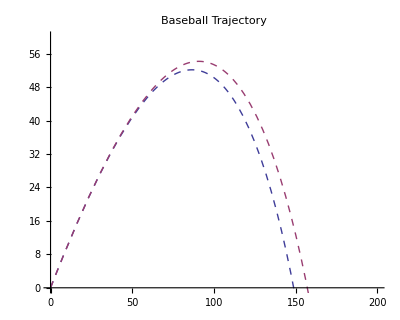

```mathematica
Cd = 0.35; ρCoors = ρ * .9; a = 0.037; m = 0.145; g = 9.8;

(* Solving case with Drag in Denver *)
baseballEqnsCoors = {x'[t] == vx[t],
y'[t]==vy[t],
 vx'[t] == -(Cd * ρCoors * π * a^2 * vx[t] * √(vx[t]^2+vy[t]^2))/(2*m),
 vy'[t] ==  -(Cd * ρCoors * π * a^2 * vy[t] * √(vx[t]^2+vy[t]^2))/(2*m) - g,
 y[0] ==0,
 x[0]==0,
 vx[0]==v0*Cos[θ0],
 vy[0]==v0*Sin[θ0]};
testBaseballCoors = {v0->60, θ0->π/4};
tminBaseballCoors = 0.0; tmaxBaseballCoors = 45.0;
solBaseballCoors = NDSolve[baseballEqnsCoors/.testBaseballCoors, {x[t], y[t], vx[t], vy[t]},{t, tminBaseballCoors, tmaxBaseballCoors}];
xposCoors = x[t]/.solBaseballCoors[[1]];
yposCoors = y[t]/.solBaseballCoors[[1]];
ParametricPlot[{Flatten[{xpos,ypos}],Flatten[{xposCoors,yposCoors}]},{t,0,10}, PlotRange->{{0,200},{0,60}}, PlotStyle->Dashed ,AspectRatio->.8, PlotLegend->{"San Diego", "Denver"}, LegendPosition->{.35,.2}, LegendSize->{.6,.5}, LegendShadow->None, PlotLabel->"Baseball Trajectory"]
```

### c.) Finding optimal angle when initial velocity is 47 m/s

```mathematica
Manipulate[Cd = 0.35; ρ = 1.2; a = 0.037; m = 0.145; g = 9.8;

(* Playing with the angle in San Diego (sea level) *)
baseballEqnsAngle = {x'[t] == vx[t],
y'[t]==vy[t],
 vx'[t] == -(Cd * ρ * π * a^2 * vx[t] * √(vx[t]^2+vy[t]^2))/(2*m),
 vy'[t] ==  -(Cd * ρ * π * a^2 * vy[t] * √(vx[t]^2+vy[t]^2))/(2*m) - g,
 y[0] ==0,
 x[0]==0,
 vx[0]==v0*Cos[θ0],
 vy[0]==v0*Sin[θ0]};
testBaseballAngle = {v0->47, θ0->(π/180*angle)};
tminBaseballAngle = 0.0; tmaxBaseballAngle = 45.0;
solBaseballAngle = NDSolve[baseballEqnsAngle/.testBaseballAngle, {x[t], y[t], vx[t], vy[t]},{t, tminBaseballAngle, tmaxBaseballAngle}];
xposAngle  = x[t]/.solBaseballAngle [[1]];
yposAngle  = y[t]/.solBaseballAngle [[1]];
dragZeroAngle =Quiet[ FindRoot[yposAngle , {t, 3}]];
howFarAngle = xposAngle /.dragZeroAngle 
, {{angle,40}, 20,60,.1}]
Print["The optimal Angle to hit the ball is ", 40 , "Degrees. This allows the ball to be hit ", howFarAngle, " m"]
```

The optimal Angle to hit the ball is 40Degrees. This allows the ball to be hit 116.945 m

The optimal Angle to hit the ball is 40Degrees. This allows the ball to be hit 116.945 m

### d.) Start with high velocity to see non-parabolic arc.

```mathematica
Manipulate[Cd = 0.35; ρ = 1.2; a = 0.037; m = 0.145; g = 9.8;

(* See it drop!! *)
baseballEqns = {x'[t] == vx[t],
y'[t]==vy[t],
 vx'[t] == -(Cd * ρ * π * a^2 * vx[t] * √(vx[t]^2+vy[t]^2))/(2*m),
 vy'[t] ==  -(Cd * ρ * π * a^2 * vy[t] * √(vx[t]^2+vy[t]^2))/(2*m) - g,
 y[0] ==0,
 x[0]==0,
 vx[0]==v0*Cos[θ0],
 vy[0]==v0*Sin[θ0]};
testBaseball = {v0->initVel, θ0->π/4};
tminBaseball = 0.0; tmaxBaseball = 60.0;
solBaseball = NDSolve[baseballEqns/.testBaseball, {x[t], y[t], vx[t], vy[t]},{t, tminBaseball, tmaxBaseball}];
xpos = x[t]/.solBaseball[[1]];
ypos = y[t]/.solBaseball[[1]];
ParametricPlot[{Flatten[{xpos,ypos}]},{t,0,15},PlotRange->{{0,475},{0,275}}, PlotStyle->Dashed ,AspectRatio->.8, PlotLabel->"Watching the Vertical Drop"]
,{{initVel,350}, 40,550}]
```

## P1.6

```mathematica
AbsoluteTiming[Total[Table[n,{n,1,10^7,1}]]][[1]]
```

3.974136